```mathematica
Dd[x_, 1, a_] := Sum[ (j+a)^0, {j,0, Floor[x-a]}]
Cc[ x_, 1, a_] := a^(-1) Dd[ x a, 1, a+1]
```

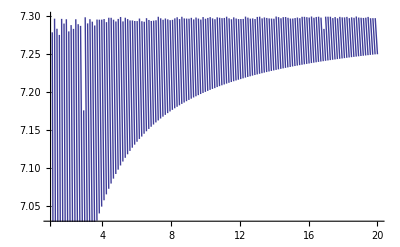

```mathematica
Plot[Cc[8.3,1,n],{n,1,20}]
```

```mathematica
Limit[ Cc[ n,1,a],a->Infinity]
```

Limit[Floor[-a+a n]/a,a→∞]

```mathematica
F[ fn_, x_, 0] := 1; F[ fn_, x_, k_] := Sum[ fn[j] F[fn, x/j, k-1],{j,1,Floor[x]}]
f[ fn_, x_, k_] := F[ fn,x,k]-F[fn,x-1,k]
FAlt[ fn_, x_, k_, t_] := Sum[ fn[j] F[fn, x/j, k-1], {j,t+1, Floor[x]}]+
Sum[ f[ fn, j, k-1] F[ fn, x/j, 1],{j,1,t}]+
Sum[ fn[s]f[fn,j,m]F[fn,x/(j s), k-m-1],{j,1,t},{s,Floor[t/j]+1,Floor[x/j]},{m,1,k-2}]
```

```mathematica
F[MoebiusMu,100,3]
```

47

```mathematica
FAlt[ MoebiusMu, 100,3,15]
```

47

```mathematica
FAlt2[ fn_, x_, k_, t_] := 
Sum[ fn[j] F[fn, x/j,k-1],{j, t+1, Floor[ x^(1/2)]}]+
Sum[ (F[fn, x/j, 1]-F[fn, x/(j+1),1])F[fn,j,k-1], {j,1,Floor[ x/Floor[x^(1/2) - 1]]}]+
Sum[ f[fn, j, k-1](F[fn, x/j, 1]-F[fn, x/(j+1),1]), {j,1,t}]+
Sum[ fn[s] f[ fn, j, m] F[ fn, x/(j s), k-m-1], {j,1,t},{s,Floor[t/j+1], Floor[Floor[ x/j]^(1/2)]}, {m,1,k-2}]+
Sum[ (F[fn,x/(j s), 1]-F[fn,x/(j(s+1)),1]) Sum[ fn[s] f[fn,j,m] F[fn,s,k-m-1],{m,1,k-2}], {j,1,t},{s,1,Floor[Floor[x/j]/Floor[Floor[x/j]^(1/2)]-1]}]
```

```mathematica
FAlt2[ MoebiusMu, 100, 3, 15]
```

33

```mathematica
FAlt3[ fn_, x_, k_, t_] := 
Sum[ fn[j] F[fn, x/j,k-1],{j, t+1, Floor[ x^(1/2)]}]+
Sum[ (F[fn, x/j, 1]-F[fn, x/(j+1),1])F[fn,j,k-1], {j,1,Floor[ x/Floor[x^(1/2) - 1]]}]+
Sum[ f[fn, j, k-1](F[fn, x/j, 1]-F[fn, x/(j+1),1]), {j,1,t}]+
Sum[ fn[s] f[ fn, j, m] F[ fn, x/(j s), k-m-1], {j,1,t},{s,Floor[t/j+1], Floor[Floor[ x/j]^(1/2)]}, {m,1,k-2}]+
Sum[ (F[fn,x/(j s), 1]-F[fn,x/(j(s+1))]) Sum[ fn[s] f[fn,j,m] F[fn,s,k-m-1],{m,1,k-2}], {j,1,t},{s,1,Floor[Floor[x/j]/Floor[Floor[x/j]^(1/2)]-1]}]
```

```mathematica
FAlt3[ MoebiusMu, 100, 3, 5]
```

37+F[MoebiusMu,5]-2 (-1-F[MoebiusMu,50/9])-F[MoebiusMu,50/7]-2 (-1-F[MoebiusMu,25/3])+F[MoebiusMu,25/3]+F[MoebiusMu,10]+2 (-2-F[MoebiusMu,25/2])+F[MoebiusMu,25/2]+F[MoebiusMu,100/7]+2 (-3-F[MoebiusMu,50/3])+F[MoebiusMu,50/3]-F[MoebiusMu,50]